```mathematica
ClearAll["Global`*"];
```

### Task & Variables

Modelling of second harmonic generation process (1550nm -> 775 nm) in periodically poled Lithium niobate crystal 1 cm long at 350 K. Find the domain length, satisfying the phase-matching conditions. Plot temperature and spectral matching curves.

```mathematica
λ0=1550×10^-9;
T0=350;
L=1;
```

### Calculation

```mathematica
no[λ_,T_]=√(4.9130+(0.1173+1.65×10^-8 T^2)/((λ×10^6)^2-(0.212+2.7×10^-8 T^2)^2)-0.0278×(λ×10^6)^2);
ne[λ_,T_]=√(4.5567+2.605×10^-7 T^2+(0.0970+2.70×10^-8 T^2)/((λ×10^6)^2-(0.201+5.4×10^-8 T^2)^2)-0.0224×(λ×10^6)^2);
```

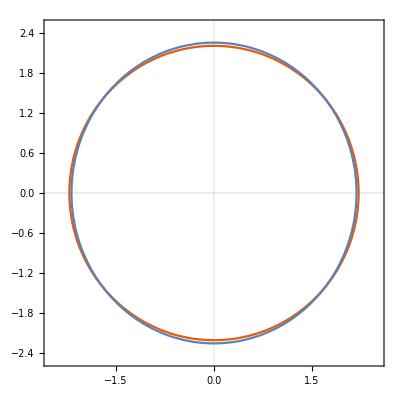

```mathematica
Show[ContourPlot[x^2/no[λ0,T0]^2+z^2/no[λ0,T0]^2==1,{x,-2.5,2.5},{z,-2.5,2.5},PlotTheme->"Scientific"],ContourPlot[x^2/ne[λ0/2,T0]^2+z^2/no[λ0/2,T0]^2==1,{x,-2.5,2.5},{z,-2.5,2.5}]]
```

```mathematica
PM[λ_,T_]:=NSolve[{x^2/no[λ,T]^2+z^2/no[λ,T]^2==x^2/ne[λ/2,T]^2+z^2/no[λ/2,T]^2==1,x>0,z>0},{x,z}];
θPM[λ_,T_]:=ArcTan[(x/.PM[λ,T][[1]])/(z/.PM[λ,T][[1]])];
```

deff[0,90] = 2.46pm/V, deff[90,0]=5.1pm/V

```mathematica
d33=25.5×10^-12;
d31=4.6×10^-12;
d22=2.1×10^-12;
d={{{0,-d22,d31},{-d22,0,0},{d31,0,0}},{{-d22,0,0},{0,d22,d31},{0,d31,0}},{{d31,0,0},{0,d31,0},{0,0,d33}}};
ee[θ_,ϕ_]:={-Cos[θ]×Cos[ϕ],-Cos[θ]×Sin[ϕ],Sin[θ]};
```

```mathematica
deff[θ_,ϕ_]:=Sum[Sum[Sum[ee[θ,ϕ][[i]]×d[[i,j,k]]×ee[θ,ϕ][[j]]×ee[θ,ϕ][[k]],{k,1,3}],{j,1,3}],{i,1,3}];
```

```mathematica
maxAngles=NMaximize[deff[θ,ϕ],{θ,ϕ}];
θ0=θ/.maxAngles[[2]];
ϕ0=ϕ/.maxAngles[[2]];
deff0=maxAngles[[1]];
```

```mathematica
θ/.maxAngles[[2]]
```

1.5708

```mathematica
NSolve[{x^2/ne[λ0,T0]^2+z^2/no[λ0,T0]^2==1,Tan[θ0]==x/z},{x,z}]
```

{}

```mathematica
(*neθ[λ_,T_,θ_]:=√((x/.NSolve[{x^2/ne[λ,T]^2+z^2/no[λ,T]^2==1,Tan[θ]==x/z},{x,z}][[1]])^2+(z/.NSolve[{x^2/ne[λ,T]^2+z^2/no[λ,T]^2==1,Tan[θ]==x/z},{x,z}][[1]])^2);*)
ne0[λ_,T_]:=ne0[λ,T]=√((x/.NSolve[{x^2/ne[λ,T]^2+z^2/no[λ,T]^2==1,Tan[θ0-10^-6]==x/z},{x,z}][[1]])^2+(z/.NSolve[{x^2/ne[λ,T]^2+z^2/no[λ,T]^2==1,Tan[θ0-10^-6]==x/z},{x,z}][[1]])^2)
```

```mathematica
ne0[λ0/2,T0]
```

2.18061

```mathematica
neθ[λ0/2,T0,π/2-10^-5]
```

neθ[31/40000000,350,-1/100000+π/2]

```mathematica
no[λ0,T0]
```

2.21288

Let’s write down phase matching conditions

```mathematica
k[λ_,T_]:=(2π)/(λ×10^2)×ne0[λ,T];
KK[λ_,T_]:=(2π)/(λ×10^2/2)×ne0[λ/2,T];
Δk[λ_,T_]:=KK[λ,T]-2k[λ,T];
(*Δk[λ_,T_]:=0;*)
σ1[λ_,T_]:=2π×k[λ,T]×(2deff0×3×10^4)/ne0[λ,T]^2;
σ2[λ_,T_]:=π×KK[λ,T]×(2deff0×3×10^4)/ne0[λ/2,T]^2;
```

The domain length is the following

```mathematica
ldom=(λ0×10^2)/(4(ne0[λ0/2,T0]-ne0[λ0,T0]))+0.00000
```

0.00094171

Equations for second harmonic generation process in periodically poled crystal

dA1/dz= -iσ1A1^* A2 (e^(-i dk z)(-1))^N
dA2/dz=-iσ2 A1^2(e^(i dk z)(-1))^N - in SGS!
N=z/ldom, A1(0)=A1^0,A2(0)=A2^0
σ1=2πke1 (χ(ω):e1e2)/(n^2(ω))
σ2=πKe1 (χ(2ω):e1e2)/(n^2(2ω))
dk=K-2k

```mathematica
(-1)^IntegerPart[0.2/ldom]
```

1

Initial values of fields A1 (1550 nm) and A2 (775 nm)

```mathematica
A10=(0.5×10^6)/(3×10^4);
A20=0;
```

```mathematica
{solsA1,solsA2}=NDSolveValue[{A1'[z]==-I×σ1[λ0,T0]×Conjugate[A1[z]]×A2[z]×Exp[-I×Δk[λ0,T0]×z]×(-1)^IntegerPart[z/ldom],A2'[z]==-I×σ2[λ0,T0]×A1[z]^2×Exp[I×Δk[λ0,T0]×z]×(-1)^IntegerPart[z/ldom],A1[0]==A10,A2[0]==A20},{A1,A2},{z,0,L}]
```

{InterpolatingFunction[{{0., 1.}}, <>],InterpolatingFunction[{{0., 1.}}, <>]}

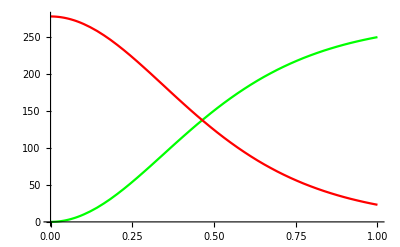

```mathematica
Show[Plot[Abs[solsA2[z]]^2,{z,0,L},PlotStyle->Green,PlotRange->All],Plot[Abs[solsA1[z]]^2,{z,0,L},PlotStyle->Red,PlotRange->All]]
```

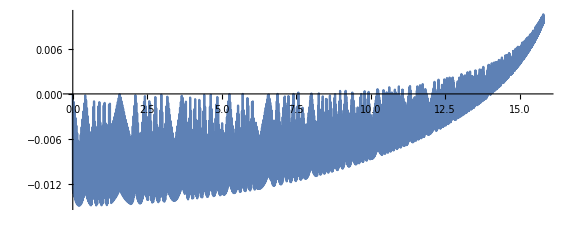

```mathematica
ParametricPlot[{Re[solsA2[z]],Im[solsA2[z]]},{z,0,L},ImageSize->Large]
```

Temperature matching

```mathematica
λexp=1567×10^-9;
solsT[T_]:=Block[{},σ1T=σ1[λexp,T];σ2T=σ2[λexp,T];ΔkT=Δk[λexp,T];solT=NDSolve[{A1T'[z]==-I×σ1T×Conjugate[A1T[z]]×A2T[z]×Exp[-I×ΔkT×z]×(-1)^IntegerPart[z/ldom],A2T'[z]==-I×σ2T×A1T[z]^2×Exp[I×ΔkT×z]×(-1)^IntegerPart[z/ldom],A1T[0]==A10,A2T[0]==A20},{A1T,A2T},{z,0,L}];resT=(Abs[A2T[L]/.solT[[1]]])^2;resT];
tableT=Table[{T,solsT[T]},{T,480,490,1}];
```

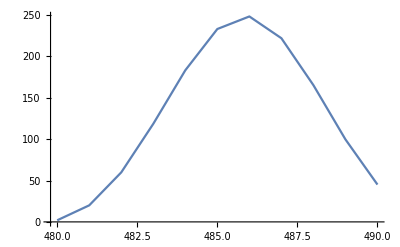

```mathematica
ListLinePlot[tableT,PlotRange->All]
```

Spectral matching

```mathematica
solsλ[λ_]:=Block[{},σ1λ=σ1[λ,T0];σ2λ=σ2[λ,T0];Δkλ=Δk[λ,T0];solλ=NDSolve[{A1λ'[z]==-I×σ1λ×Conjugate[A1λ[z]]×A2λ[z]×Exp[-I×Δkλ×z]×(-1)^IntegerPart[z/ldom],A2λ'[z]==-I×σ2λ×A1λ[z]^2×Exp[I×Δkλ×z]×(-1)^IntegerPart[z/ldom],A1λ[0]==A10,A2λ[0]==A20},{A1λ,A2λ},{z,0,L}];resλ=(Abs[A2λ[L]/.solλ[[1]]])^2;resλ];
tableλ=Table[{λ,solsλ[λ]},{λ,1.54×10^-6,1.56×10^-6,0.001×10^-6}];
```

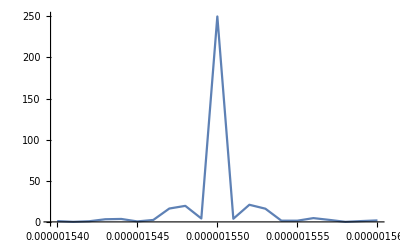

```mathematica
ListLinePlot[tableλ,PlotRange->All]
```